# Análisis de Ciclos

## Cantidad de ciclos presentes en las redes generadas por el modelo a través de diferentes valores:

### People = 10, 50, 100, 500, 1000 Time = 100, 250, 1000, 5000, 10000 Capacity = 5 Cycle Length = 3

## Variables:

```mathematica
people={10,50,100,500,1000};
```

```mathematica
time={100,250,1000,5000,10000};
```

```mathematica
capacity=5;
```

## Carga de las redes

```mathematica
SetDirectory[NotebookDirectory[]];
```

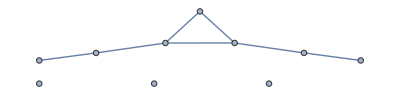
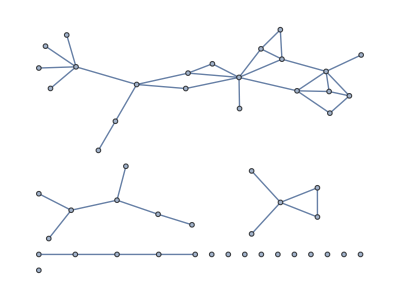
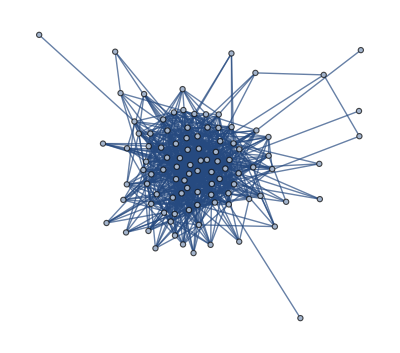
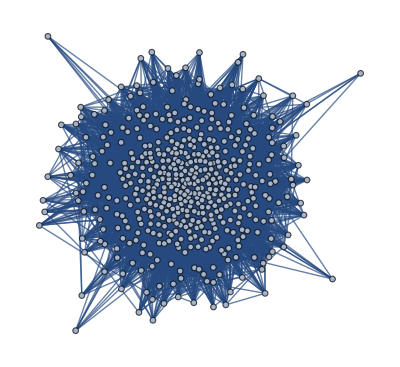
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
redes=Table[Import[StringJoin["Redes/Ciclos/network-",IntegerString[people[[i]]],"-5-",IntegerString[time[[i]]],".g6"]],{i,1,Length[people],1}]
```

```mathematica
Length[FindCycle[redes[[5]],3,All]]
```

## Función para crear red aleatoria con la misma cantidad de nodos y enlaces que las redes generadas por el modelo

```mathematica
randomizeGraph[g_]:=Module[{randGraph},
randGraph=RandomGraph[{VertexCount[g],EdgeCount[g]}];
Return[randGraph];
];
```

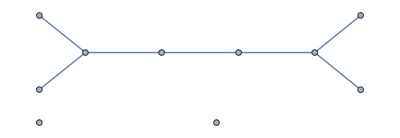
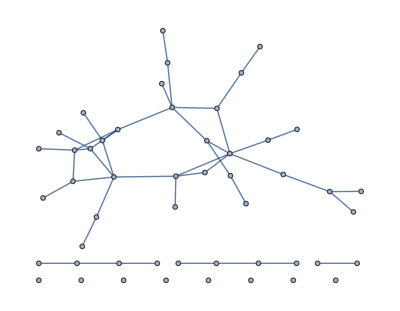
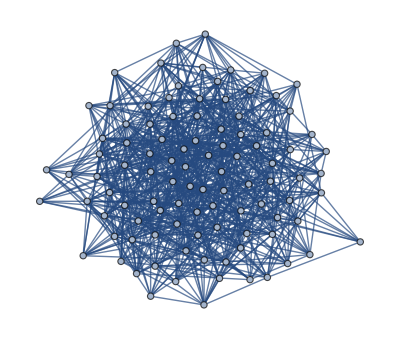
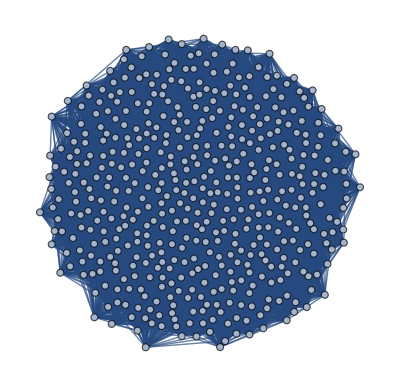
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aleatorias=Map[randomizeGraph,redes]
```

```mathematica
EdgeCount[redes[[5]]]
```

73249

```mathematica
Reap[Sow[FindCycle[redes[[4]],3,All]]];//AbsoluteTiming
```

{34.2704,Null}

```mathematica
FindCycle[redes[[5]],3,All];//AbsoluteTiming
```

{1115.05,Null}

## # de ciclos de longitud 3 presentes en las redes generadas por el modelo en las diferentes configuraciones

```mathematica
ciclosRedesModelo=Table[Length[FindCycle[redes[[i]],3,All]],{i,1,Length[people],1}];//AbsoluteTiming
```

{745.216,Null}

## # de ciclos de longitud 3 presentes en las redes aleatorias de configuraciones similares a las del modelo

```mathematica
ciclosRedesAleatorias=Table[Length[FindCycle[aleatorias[[i]],3,All]],{i,1,Length[people],1}];//AbsoluteTiming
```

{801.45,Null}

## Grafica people vs # de ciclos de longitud 3

```mathematica
unidosCiclos=Partition[Join[ciclosRedesModelo,ciclosRedesAleatorias],5];
```

```mathematica
dataPlot=Table[Table[{people[[t]],unidosCiclos[[k,t]]},{t,1,Length[people],1}],{k,1,2,1}];
```

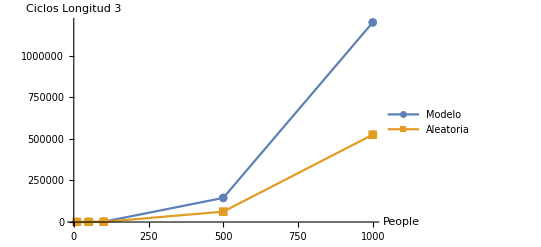

```mathematica
ListLinePlot[dataPlot,PlotLegends->{"Modelo","Aleatoria"},AxesLabel->{"People","Ciclos Longitud 3"},PlotMarkers->Automatic]
```

```mathematica
unidosCiclos
```

{{1,6,1751,144856,1199392},{0,2,751,62368,524729}}

## Análisis comparativo de las medidas de diámetro, longitud de caminos promedio y clustering coefficient.

```mathematica
aleatorias={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## Las variables people y time; serán las mismas configuradas en el análisis anterior de ciclos.

### Cálculo de los diámetros de las redes

```mathematica
diametrosRedesModelo=Map[GraphDiameter,redes];
```

```mathematica
diametrosRedesAleatorias=Map[GraphDiameter,aleatorias];
```

```mathematica
unidosDiametros={diametrosRedesModelo,diametrosRedesAleatorias};
unidosDiametros
```

{{∞,∞,4,3,3},{∞,∞,3,3,2}}

## Gráfica People vs Diámetro

```mathematica
dataDiameterPlot=Table[Table[{people[[t]],unidosDiametros[[k,t]]},{t,1,Length[people],1}],{k,1,2,1}];
```

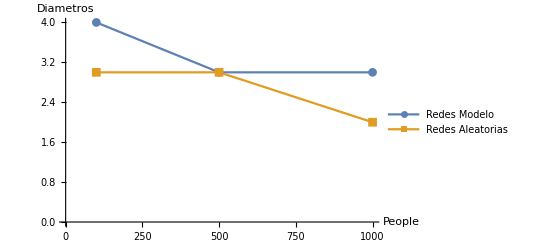

```mathematica
ListLinePlot[dataDiameterPlot,PlotLegends->{"Redes Modelo","Redes Aleatorias"},AxesLabel->{"People","Diametros"},PlotMarkers->Automatic]
```

## Longitud de camino promedio (Average Path Length)

### Cálculo de los caminos promedios de las redes

```mathematica
unidosApl={Map[MeanGraphDistance,redes],Map[MeanGraphDistance,aleatorias]};
```

```mathematica
N[unidosApl]
```

{{∞,∞,2.02162,1.87475,1.85908},{∞,∞,1.88727,1.85556,1.85336}}

## Grafica people vs APL

```mathematica
dataAplPlot=Table[Table[{people[[t]],unidosApl[[k,t]]},{t,1,Length[people],1}],{k,1,2,1}];
```

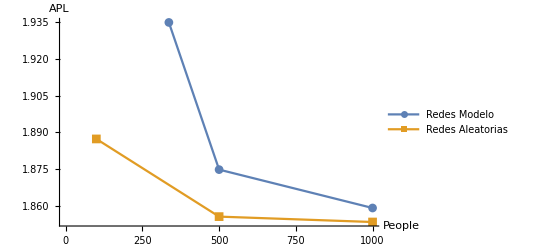

```mathematica
ListLinePlot[dataAplPlot,PlotLegends->{"Redes Modelo","Redes Aleatorias"},AxesLabel->{"People","APL"},PlotMarkers->Automatic]
```

## Clustering Coefficient

```mathematica
unidosClustCoeff={Map[GlobalClusteringCoefficient,redes],Map[GlobalClusteringCoefficient,aleatorias]};
```

```mathematica
N[unidosClustCoeff]
```

{{0.333333,0.191489,0.304222,0.259038,0.260998},{0.,0.0705882,0.169309,0.144215,0.146837}}

## Gráfica People vs Clustering Coefficient

```mathematica
dataClustCoeffPlot=Table[Table[{people[[t]],unidosClustCoeff[[k,t]]},{t,1,Length[people],1}],{k,1,2,1}];
```

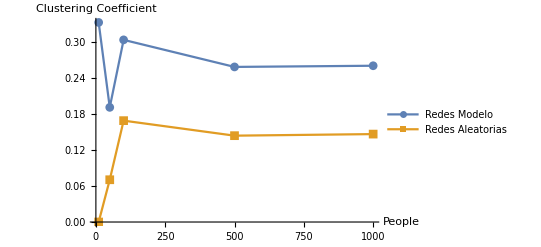

```mathematica
ListLinePlot[dataClustCoeffPlot,PlotLegends->{"Redes Modelo","Redes Aleatorias"},AxesLabel->{"People","Clustering Coefficient"},PlotMarkers->Automatic]
```

## Análisis usando redes grandes

Función que recibe como entrada un grafo y devuelve la cantidad de ciclos de longitud 3 presentes en él

```mathematica
nGC3[g_]:=Module[{adjmatrix,matrix3,amountResult},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
amountResult=Tr[matrix3]/6;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 4

```mathematica
nGC4[g_]:=Module[{adjmatrix,matrix4, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix4=MatrixPower[adjmatrix,4];sumatoria=Sum[(VertexDegree[g,i]*(VertexDegree[g,i]-1)),{i,VertexCount[g]}];
amountResult=(Tr[matrix4]-(2*sumatoria)-(2*EdgeCount[g]))/8;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 5

```mathematica
nGC5[g_]:=Module[{adjmatrix,matrix3,matrix5, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
matrix5=MatrixPower[adjmatrix,5];sumatoria=Sum[matrix3[[i]][[i]]*(VertexDegree[g,i]-2),{i,VertexCount[g]}];
amountResult=(Tr[matrix5]-(5*sumatoria)-(5*Tr[matrix3]))/10;
Return[amountResult]
];
```

#### Comparación de la red más grande del modelo frente a una aleatoria de mismas proporciones

```mathematica
redMayorModelo = redes[[5]];
```

```mathematica
redMayorAleato = aleatorias[[5]];
```

```mathematica
ciclosModeloPlot = {{3,nGC3[redMayorModelo]},{4,nGC4[redMayorModelo]},{5,nGC5[redMayorModelo]}};
```

```mathematica
ciclosAleatoPlot = {{3,nGC3[redMayorAleato]},{4,nGC4[redMayorAleato]},{5,nGC5[redMayorAleato]}};
```

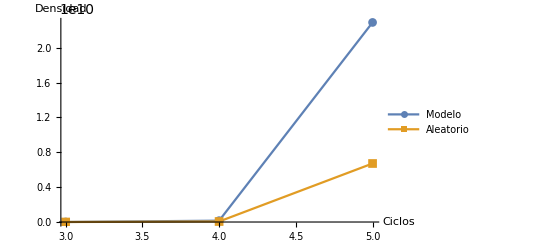

```mathematica
ListLinePlot[{ciclosModeloPlot,ciclosAleatoPlot},PlotLegends->{"Modelo","Aleatorio"},AxesLabel->{"Ciclos","Densidad"},PlotMarkers->Automatic]
```

```mathematica
ciclosAleatoPlot
```

{{3,524729},{4,57468417},{5,6715552405}}

```mathematica
ciclosModeloPlot
```

{{3,1199392},{4,154245988},{5,22906076351}}

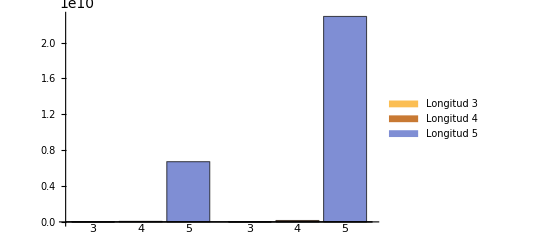

```mathematica
BarChart[{{524729,57468417,6715552405},{1199392,154245988,22906076351}},ChartLabels->{"3","4","5"},ChartLegends->{"Longitud 3","Longitud 4","Longitud 5"}]
```